```mathematica
<< "/home/pablo/Escritorio/Uni/RRT/drawTx.m"
<< "/home/pablo/Escritorio/Uni/RRT/RandomData.m"
```

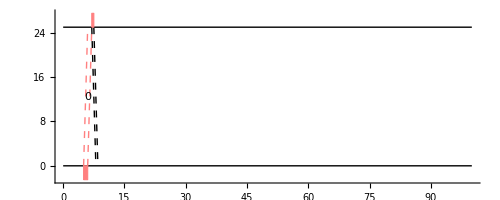

```mathematica
tTrans=1;
longResp=0.5;
SetIniParDraw[tTrans,longResp];
a={5,9600,0,0,0};
Show[DrawWin[0,100,8],DrawPacketTx[a]]
```

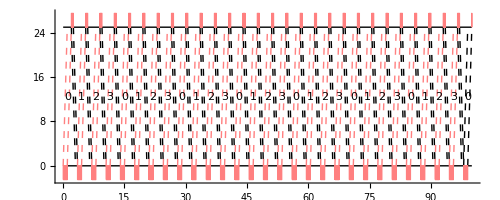

```mathematica
longPck=9600;
lstPck=Table[{n*(2*tTrans+longResp+longPck/9600),longPck,n,0,0},{n,0,50}];
Show[DrawWin[0,100,4],Map[DrawPacketTx[#]&,lstPck]]
Manipulate[Show[DrawWin[origin,ww,4],Map[DrawPacketTx[#]&,lstPck]],{origin,0,100-ww},{ww,10,50}]
```

```mathematica
FifoSchedulling[arrivals_,service_]:=Module[{n,checkTime},n=1;checkTime=arrivals[[1]];
Map[(If[checkTime>=#,checkTime+=service[[n++]],checkTime=#+service[[n++]]])&,arrivals]]
```

```mathematica
InsertionTimeCal[depar_,serv_]:=
Module[{i,inserTime},
i=0;
inserTime={};
For[i=0,i<Length[depar],i++;inserTime=Join[inserTime,{depar[[i]]-serv[[i]]}]];
Return[inserTime]
]
```

```mathematica
lamda=70;mu=100;numPaquetes=100;
InterArrivalsTime=Table[RandomExp[lamda],numPaquetes];
ArrivalsTime=Accumulate[InterArrivalsTime];
ServTime=Table[RandomExp[mu],numPaquetes];
DeparturesTimes=FifoSchedulling[ArrivalsTime,ServTime];
InsertionTime=InsertionTimeCal[DeparturesTimes,ServTime];
tprop=0.05;tack=0.004;
```

```mathematica
CalculoPaquetes[insertionTime_,servTime_,N_]:=
Module[{n,paquetes,i},
n=0;
paquetes={};
For[i=0,i<Length[insertionTime],
i++;paquetes=Join[paquetes,{insertionTime[[i]],9600*servTime[[i]],n,0,0}];
If[n==N-1,n=0,n++];
];
Return[Partition[paquetes,5]]
]
```